## rBRSSS

### preliminaries

```mathematica
Clear[Ceta,Cpi,Clambda]
```

```mathematica
ee1=t eps'[t]+4/3 eps[t]-phi[t]
```

(4 eps[t])/3-phi[t]+t eps'[t]

```mathematica
ee2=-tp phi'[t]+4/3 eta/t-phi[t]-4/3 tp/t phi[t]-l1/2/eta^2 phi[t]^2
```

(4 eta)/(3 t)-phi[t]-(4 tp phi[t])/(3 t)-(l1 phi[t]^2)/(2 eta^2)-tp phi'[t]

```mathematica
Solve[ee2==0,phi'[t]]
```

{{phi'[t]→(8 eta^3-6 eta^2 t phi[t]-8 eta^2 tp phi[t]-3 l1 t phi[t]^2)/(6 eta^2 t tp)}}

```mathematica
m1=(D[ee1,t]/.%)[[1]]
```

-(8 eta^3-6 eta^2 t phi[t]-8 eta^2 tp phi[t]-3 l1 t phi[t]^2)/(6 eta^2 t tp)+(7 eps'[t])/3+t eps''[t]

```mathematica
rep1={eps'[t]->4/t eps[t](f[w[t]]-1)}
```

{eps'[t]→(4 eps[t] (-1+f[w[t]]))/t}

```mathematica
rep2={eps'[t]->4/t eps[t](f[w[t]]-1),eps''[t]->(4 eps[t] (5+4 f[w[t]]^2+f[w[t]] (-9+w[t] f'[w[t]])))/t^2}
```

{eps'[t]→(4 eps[t] (-1+f[w[t]]))/t,eps''[t]→(4 eps[t] (5+4 f[w[t]]^2+f[w[t]] (-9+w[t] f'[w[t]])))/t^2}

```mathematica
rr4=(Solve[ee1==0,phi[t]]/.rep2)[[1]]
```

{phi[t]→1/3 (4 eps[t]+12 eps[t] (-1+f[w[t]]))}

```mathematica
rep3=Join[rep2,rr4]
```

{eps'[t]→(4 eps[t] (-1+f[w[t]]))/t,eps''[t]→(4 eps[t] (5+4 f[w[t]]^2+f[w[t]] (-9+w[t] f'[w[t]])))/t^2,phi[t]→1/3 (4 eps[t]+12 eps[t] (-1+f[w[t]]))}

```mathematica
s1={eta->4/3Ceta eps[t]/T,tp->Cpi/T,l1->4/3 eps[t]Ceta Clambda Cpi/T^2}
```

{eta→(4 Ceta eps[t])/(3 T),tp→Cpi/T,l1→(4 Ceta Clambda Cpi eps[t])/(3 T^2)}

```mathematica
Expand[(Expand[m1/.rep3]/.s1/.T->w/t)/eps[t]/4 t Cpi]/.Clambda->0
```

-(4 Ceta)/9+(16 Cpi)/9-(2 w)/3-16/3 Cpi f[w[t]]+w f[w[t]]+4 Cpi f[w[t]]^2+Cpi f[w[t]] w[t] f'[w[t]]

```mathematica
Expand[(Expand[m1/.rep3]/.s1/.T->w/t)/eps[t]/4 t Cpi]
```

-(4 Ceta)/9+(16 Cpi)/9-(2 w)/3+(2 Clambda Cpi w)/(3 Ceta)-16/3 Cpi f[w[t]]+w f[w[t]]-(2 Clambda Cpi w f[w[t]])/Ceta+4 Cpi f[w[t]]^2+(3 Clambda Cpi w f[w[t]]^2)/(2 Ceta)+Cpi f[w[t]] w[t] f'[w[t]]

```mathematica
w[t_]=t
```

t

```mathematica
eq=Expand[(Expand[m1/.rep3]/.s1/.T->w/t)/eps[t]/4 t Cpi]/.t->w
```

-(4 Ceta)/9+(16 Cpi)/9-(2 w)/3+(2 Clambda Cpi w)/(3 Ceta)-16/3 Cpi f[w]+w f[w]-(2 Clambda Cpi w f[w])/Ceta+4 Cpi f[w]^2+(3 Clambda Cpi w f[w]^2)/(2 Ceta)+Cpi w f[w] f'[w]

### Attractors low order approximations

```mathematica
Ceta=1;Clambda=0;Cpi=5 Ceta;
```

```mathematica
Clear[f,fa1,fa2]
```

```mathematica
fa1[w_]=f[w]/.Simplify[Solve[0==eq/.f'[w]->0,f[w]]][[2]]
```

1/120 (80-3 w+√(320+9 w^2))

```mathematica
f[w_]:=fa1[w]+df[w]
```

```mathematica
fa2[w_]=fa1[w]+df[w]/.Solve[0==eq/.df'[w]->0,df[w]][[2]]
```

1/120 (80-3 w+√(320+9 w^2))+1/40 (w/8-(3 w^2)/(8 √(320+9 w^2))-1/3 √(320+9 w^2)+1/24 √(3840 w-135 w^2+(81 w^4)/(320+9 w^2)-(11520 w^2)/(√(320+9 w^2))+(378 w^3)/(√(320+9 w^2))+64 (320+9 w^2)))

```mathematica
f[w_]:=fa2[w]+df[w]
```

```mathematica
fa3[w_]=fa2[w]+df[w]/.NSolve[0==eq/.df'[w]->0,df[w]][[2]]
```

1/120 (80-3 w+√(320+9 w^2))+1/40 (w/8-(3 w^2)/(8 √(320+9 w^2))-1/3 √(320+9 w^2)+1/24 √(3840 w-135 w^2+(81 w^4)/(320+9 w^2)-(11520 w^2)/(√(320+9 w^2))+(378 w^3)/(√(320+9 w^2))+64 (320+9 w^2)))+0.025 (3.55271×10^-15-0.015625 w-(0.421875 w^4)/((320.+9. w^2)^(3/2))+(0.46875 w^2)/(√(320.+9. w^2))-(10. w)/(√(20480.+3840. w+441. w^2+(81. w^4)/(320.+9. w^2)-(11520. w^2)/(√(320.+9. w^2))+(378. w^3)/(√(320.+9. w^2))))-(2.29688 w^2)/(√(20480.+3840. w+441. w^2+(81. w^4)/(320.+9. w^2)-(11520. w^2)/(√(320.+9. w^2))+(378. w^3)/(√(320.+9. w^2))))+(3.79688 w^6)/((320.+9. w^2)^2 √(20480.+3840. w+441. w^2+(81. w^4)/(320.+9. w^2)-(11520. w^2)/(√(320.+9. w^2))+(378. w^3)/(√(320.+9. w^2))))-(270. w^4)/((320.+9. w^2)^(3/2) √(20480.+3840. w+441. w^2+(81. w^4)/(320.+9. w^2)-(11520. w^2)/(√(320.+9. w^2))+(378. w^3)/(√(320.+9. w^2))))+(8.85938 w^5)/((320.+9. w^2)^(3/2) √(20480.+3840. w+441. w^2+(81. w^4)/(320.+9. w^2)-(11520. w^2)/(√(320.+9. w^2))+(378. w^3)/(√(320.+9. w^2))))-(0.84375 w^4)/((320.+9. w^2) √(20480.+3840. w+441. w^2+(81. w^4)/(320.+9. w^2)-(11520. w^2)/(√(320.+9. w^2))+(378. w^3)/(√(320.+9. w^2))))+(60. w^2)/(√(320.+9. w^2) √(20480.+3840. w+441. w^2+(81. w^4)/(320.+9. w^2)-(11520. w^2)/(√(320.+9. w^2))+(378. w^3)/(√(320.+9. w^2))))-(2.95313 w^3)/(√(320.+9. w^2) √(20480.+3840. w+441. w^2+(81. w^4)/(320.+9. w^2)-(11520. w^2)/(√(320.+9. w^2))+(378. w^3)/(√(320.+9. w^2))))-0.0416667 √(20480.+3840. w+441. w^2+(81. w^4)/(320.+9. w^2)-(11520. w^2)/(√(320.+9. w^2))+(378. w^3)/(√(320.+9. w^2)))+√((-3.55271×10^-15+0.015625 w+(0.421875 w^4)/((320.+9. w^2)^(3/2))-(0.46875 w^2)/(√(320.+9. w^2))+(10. w)/(√(20480.+3840. w+441. w^2+(81. w^4)/(320.+9. w^2)-(11520. w^2)/(√(320.+9. w^2))+(378. w^3)/(√(320.+9. w^2))))+(2.29688 w^2)/(√(20480.+3840. w+441. w^2+(81. w^4)/(320.+9. w^2)-(11520. w^2)/(√(320.+9. w^2))+(378. w^3)/(√(320.+9. w^2))))-(3.79688 w^6)/((320.+9. w^2)^2 √(20480.+3840. w+441. w^2+(81. w^4)/(320.+9. w^2)-(11520. w^2)/(√(320.+9. w^2))+(378. w^3)/(√(320.+9. w^2))))+(270. w^4)/((320.+9. w^2)^(3/2) √(20480.+3840. w+441. w^2+(81. w^4)/(320.+9. w^2)-(11520. w^2)/(√(320.+9. w^2))+(378. w^3)/(√(320.+9. w^2))))-(8.85938 w^5)/((320.+9. w^2)^(3/2) √(20480.+3840. w+441. w^2+(81. w^4)/(320.+9. w^2)-(11520. w^2)/(√(320.+9. w^2))+(378. w^3)/(√(320.+9. w^2))))+(0.84375 w^4)/((320.+9. w^2) √(20480.+3840. w+441. w^2+(81. w^4)/(320.+9. w^2)-(11520. w^2)/(√(320.+9. w^2))+(378. w^3)/(√(320.+9. w^2))))-(60. w^2)/(√(320.+9. w^2) √(20480.+3840. w+441. w^2+(81. w^4)/(320.+9. w^2)-(11520. w^2)/(√(320.+9. w^2))+(378. w^3)/(√(320.+9. w^2))))+(2.95313 w^3)/(√(320.+9. w^2) √(20480.+3840. w+441. w^2+(81. w^4)/(320.+9. w^2)-(11520. w^2)/(√(320.+9. w^2))+(378. w^3)/(√(320.+9. w^2))))+0.0416667 √(20480.+3840. w+441. w^2+(81. w^4)/(320.+9. w^2)-(11520. w^2)/(√(320.+9. w^2))+(378. w^3)/(√(320.+9. w^2))))^2-80. (-1.66533×10^-16+0.0208333 w+0.00205078 w^2-(0.00791016 w^6)/((320.+9. w^2)^2)+(0.5625 w^4)/((320.+9. w^2)^(3/2))-(0.018457 w^5)/((320.+9. w^2)^(3/2))+(0.00527344 w^4)/(320.+9. w^2)-(0.375 w^2)/(√(320.+9. w^2))+(0.0131836 w^3)/(√(320.+9. w^2))+(6.66667 w)/(√(20480.+3840. w+441. w^2+(81. w^4)/(320.+9. w^2)-(11520. w^2)/(√(320.+9. w^2))+(378. w^3)/(√(320.+9. w^2))))+(1.3125 w^2)/(√(20480.+3840. w+441. w^2+(81. w^4)/(320.+9. w^2)-(11520. w^2)/(√(320.+9. w^2))+(378. w^3)/(√(320.+9. w^2))))-(0.0502441 w^3)/(√(20480.+3840. w+441. w^2+(81. w^4)/(320.+9. w^2)-(11520. w^2)/(√(320.+9. w^2))+(378. w^3)/(√(320.+9. w^2))))+(0.0355957 w^8)/((320.+9. w^2)^(5/2) √(20480.+3840. w+441. w^2+(81. w^4)/(320.+9. w^2)-(11520. w^2)/(√(320.+9. w^2))+(378. w^3)/(√(320.+9. w^2))))-(5.0625 w^6)/((320.+9. w^2)^2 √(20480.+3840. w+441. w^2+(81. w^4)/(320.+9. w^2)-(11520. w^2)/(√(320.+9. w^2))+(378. w^3)/(√(320.+9. w^2))))+(0.166113 w^7)/((320.+9. w^2)^2 √(20480.+3840. w+441. w^2+(81. w^4)/(320.+9. w^2)-(11520. w^2)/(√(320.+9. w^2))+(378. w^3)/(√(320.+9. w^2))))+(180. w^4)/((320.+9. w^2)^(3/2) √(20480.+3840. w+441. w^2+(81. w^4)/(320.+9. w^2)-(11520. w^2)/(√(320.+9. w^2))+(378. w^3)/(√(320.+9. w^2))))-(11.8125 w^5)/((320.+9. w^2)^(3/2) √(20480.+3840. w+441. w^2+(81. w^4)/(320.+9. w^2)-(11520. w^2)/(√(320.+9. w^2))+(378. w^3)/(√(320.+9. w^2))))+(0.185889 w^6)/((320.+9. w^2)^(3/2) √(20480.+3840. w+441. w^2+(81. w^4)/(320.+9. w^2)-(11520. w^2)/(√(320.+9. w^2))+(378. w^3)/(√(320.+9. w^2))))+(1.125 w^4)/((320.+9. w^2) √(20480.+3840. w+441. w^2+(81. w^4)/(320.+9. w^2)-(11520. w^2)/(√(320.+9. w^2))+(378. w^3)/(√(320.+9. w^2))))-(0.0461426 w^5)/((320.+9. w^2) √(20480.+3840. w+441. w^2+(81. w^4)/(320.+9. w^2)-(11520. w^2)/(√(320.+9. w^2))+(378. w^3)/(√(320.+9. w^2))))-(40. w^2)/(√(320.+9. w^2) √(20480.+3840. w+441. w^2+(81. w^4)/(320.+9. w^2)-(11520. w^2)/(√(320.+9. w^2))+(378. w^3)/(√(320.+9. w^2))))+(3.1875 w^3)/(√(320.+9. w^2) √(20480.+3840. w+441. w^2+(81. w^4)/(320.+9. w^2)-(11520. w^2)/(√(320.+9. w^2))+(378. w^3)/(√(320.+9. w^2))))-(0.0861328 w^4)/(√(320.+9. w^2) √(20480.+3840. w+441. w^2+(81. w^4)/(320.+9. w^2)-(11520. w^2)/(√(320.+9. w^2))+(378. w^3)/(√(320.+9. w^2))))-3.46945×10^-18 √(20480.+3840. w+441. w^2+(81. w^4)/(320.+9. w^2)-(11520. w^2)/(√(320.+9. w^2))+(378. w^3)/(√(320.+9. w^2)))+0.000016276 w √(20480.+3840. w+441. w^2+(81. w^4)/(320.+9. w^2)-(11520. w^2)/(√(320.+9. w^2))+(378. w^3)/(√(320.+9. w^2)))+(0.000439453 w^4 √(20480.+3840. w+441. w^2+(81. w^4)/(320.+9. w^2)-(11520. w^2)/(√(320.+9. w^2))+(378. w^3)/(√(320.+9. w^2))))/((320.+9. w^2)^(3/2))-(0.000488281 w^2 √(20480.+3840. w+441. w^2+(81. w^4)/(320.+9. w^2)-(11520. w^2)/(√(320.+9. w^2))+(378. w^3)/(√(320.+9. w^2))))/(√(320.+9. w^2)))))

### Numerical initial data

```mathematica
Clear[f]
```

```mathematica
ms2[w_]=Table[f[w]/.NDSolve[{eq==0,f[0.1]==f0},f[w],{w,0.1,5}][[1]],{f0,0.6,4,0.1}]
```

{InterpolatingFunction[{{0.1, 5.}}, <>][w],InterpolatingFunction[{{0.1, 5.}}, <>][w],InterpolatingFunction[{{0.1, 5.}}, <>][w],InterpolatingFunction[{{0.1, 5.}}, <>][w],InterpolatingFunction[{{0.1, 5.}}, <>][w],InterpolatingFunction[{{0.1, 5.}}, <>][w],InterpolatingFunction[{{0.1, 5.}}, <>][w],InterpolatingFunction[{{0.1, 5.}}, <>][w],InterpolatingFunction[{{0.1, 5.}}, <>][w],InterpolatingFunction[{{0.1, 5.}}, <>][w],InterpolatingFunction[{{0.1, 5.}}, <>][w],InterpolatingFunction[{{0.1, 5.}}, <>][w],InterpolatingFunction[{{0.1, 5.}}, <>][w],InterpolatingFunction[{{0.1, 5.}}, <>][w],InterpolatingFunction[{{0.1, 5.}}, <>][w],InterpolatingFunction[{{0.1, 5.}}, <>][w],InterpolatingFunction[{{0.1, 5.}}, <>][w],InterpolatingFunction[{{0.1, 5.}}, <>][w],InterpolatingFunction[{{0.1, 5.}}, <>][w],InterpolatingFunction[{{0.1, 5.}}, <>][w],InterpolatingFunction[{{0.1, 5.}}, <>][w],InterpolatingFunction[{{0.1, 5.}}, <>][w],InterpolatingFunction[{{0.1, 5.}}, <>][w],InterpolatingFunction[{{0.1, 5.}}, <>][w],InterpolatingFunction[{{0.1, 5.}}, <>][w],InterpolatingFunction[{{0.1, 5.}}, <>][w],InterpolatingFunction[{{0.1, 5.}}, <>][w],InterpolatingFunction[{{0.1, 5.}}, <>][w],InterpolatingFunction[{{0.1, 5.}}, <>][w],InterpolatingFunction[{{0.1, 5.}}, <>][w],InterpolatingFunction[{{0.1, 5.}}, <>][w],InterpolatingFunction[{{0.1, 5.}}, <>][w],InterpolatingFunction[{{0.1, 5.}}, <>][w],InterpolatingFunction[{{0.1, 5.}}, <>][w],InterpolatingFunction[{{0.1, 5.}}, <>][w]}

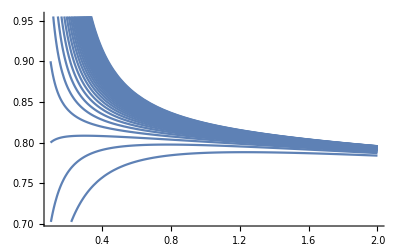

```mathematica
Show[Plot[{ms2[w]},{w,0.1,2},PlotStyle->{{},{RGBColor[1,0,0]},{RGBColor[0,0,0]}}]]
```

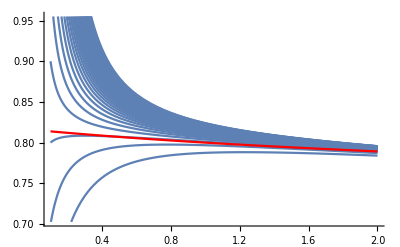

```mathematica
Show[Plot[{ms2[w]},{w,0.1,2},PlotStyle->{{},{RGBColor[1,0,0]},{RGBColor[0,0,0]}}],Plot[fa3[w],{w,0.1,2},PlotStyle->RGBColor[1,0,0]]]
```